# Explorations in Brownian Motion

## Project Heuristics

#### What is this Project?

A glimpse into the world of random particulate behaviour, moving into its applications in the financial world, culminating in some interactive tools and animations to better visualise the random process in both 2 - D and 3 - D.

An Overview into the Deep Dive ...

#### Stochastic Processes

In the most simple terms, a stochastic process is a series of Random Variables.

Brownian Motion

A physical phenomena that was first documented thought the observation of pollen particles by Botanist Robert Brown . In particular, it was noted that they appeared to move randomly, despite gravities effects . This both indirectly confirmed the existence of gas molecules, and allows for us to model the movement of a dust particle as essentially random .
  
Mathematically, we model the position of such a particle in space as time evolves using a stochastic process .
  
A natural assumption to make about such a process is that the movement of the particle is continuous, and that between two observations not too distant from each - other, the particle has not moved too much . This roughly translates to what we know as a normal disruption, with some mean position .

Intermediate Tools and Terms

In order to get a feel for how we can covert these ideas into actionable Mathematics, and then code, we’ll take a quick look at the tools and Terms necessary for such a transformation of information.

Taylor Expansion: Allows for us to marry Stochastic Processes and Analysis/Calculus (Ito Calculus).

Wiener-Process: Essentially  a technical synonym for Brownian Motion.

Geometric Brownian Motion: Mirrors a Wiener-Process, with the important difference that we include an extra term so that it is an increasing function.

## Itô’s Calculus and Brownian Motion

#### Calculus on Stochastic Processes

As mentioned before, we are going to model the movement of a dust particle surrounded by gas with a random distribution over time, but also with an assumption continuity. We call this a wiener process, and it has the following form.

W_0 = 0.

∀ t > 0, [W_(t+u)- W_t ] and [W_s], are independent, where s ⩽ t and u ⩾ 0.

W_(t+u)- W_t  ∼  𝒩(0, u).

W_tis continuous in t.

In the language of dust particles, this is naturally leads to process

Χ_t = μt + σW_t

were μ and σ^2 represent the average position and the spread of the dust particle (respectively).

For a general f(x) rather than X_t, we can apply a Taylor expansion:

df =(∂_t f)dt + (∂_x f)dx + (1/2(∂^2)_(x^2)f)dx^2+...

Substituting X_t for x, and therefore μt + σW_t for d_x

df=(∂_t f)dt + ∂_x f(μt+σ W_t)+ 1/2(∂^2)_(x^2)f(μt+σ W_t)^2+...

And as dt → 0, we find that (∵Quadratic invariance of Wiener Process)

df = (∂_t f + μ ∂_x f+  σ^2/2(∂^2)_(x^2)f)dt + (σ∂_x f)dW_t

In  our example, we note that with

f(X_t) = log(X_t)

Then after some algebra

X_t= X_0 exp( σ W_t -σ^2/2 t) , (1)

So, in code, we could use the following example

(Note that we have ignored the μ term, as the mean for a Brownian motion particle should be its starting position)

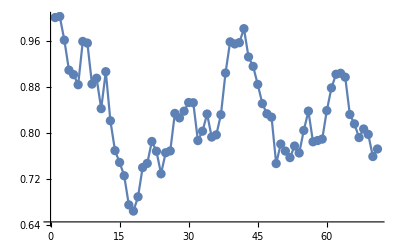

```mathematica
(* starting position *)
s0=1;
(* set small time-step *)
dt=0.001;
(* set arbitrary variance *)
sigma=1.4;
(* how many points are we interesting in simulating? *)
sampleSize=70;
(* generate data based on (1) *)
sigSqr=-sigma^2/2*dt;
randNormx=Table[sigma*z,{z,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}];
expx=Exp[sigSqr+randNormx];
preProcessx=Prepend[expx,1];
patternsx=Table[s0*x,{x,Rest[FoldList[Times,1,preProcessx]]}];
(* plot generated data *)
ListLinePlot[patternsx,Mesh->All]
```

## Geometric Brownian Motion

### An application of Brownian Motion

Trade between parties on a mass scale is inherently random, as far a we can tell.

For a long time high finance has been utilising Brownian Motion in order to try to model the economy.

The big (yet minor) difference between Geometric Brownian Motion and Brownian motion is the drift term (μ), which for Brownian motion is 0, but it is not so for Geometric Brownian motion.

The idea here is to simulate a mostly increasing function with random local behaviour.

Lets look at an example

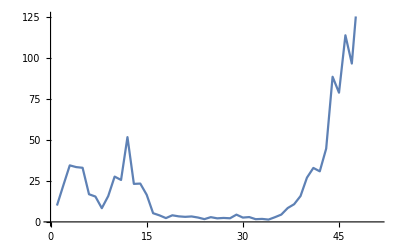

```mathematica
mu=1;
s0=10;
dt=0.1;
sigma=1.4;
sampleSize=50;
sigSqr=(mu-sigma^2/2)*dt;
randNormx=Table[sigma*z,{z,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}];
expx=Exp[sigSqr+randNormx];
preProcessx=Prepend[expx,1];
patternsx=Table[s0*x,{x,Rest[FoldList[Times,1,preProcessx]]}];
ListLinePlot[patternsx]
```

## Moving into 3D

### The 3-D Wiener Process (Wiener Sausage)

A simple extension of the 2-D Brownian motion formulation, we simple add another dimension to our calculations that inherits a data set from a different set of Random Variables with the same mean and Variance. 

The idea essential idea here is that influences on movement x and y of the dust particle are independent.

In code, this looks like the following:

```mathematica
s0=10;
dt=0.001;
sigma=1.4;
sampleSize=70;
sigSqr=-sigma^2/2*dt;
(* here we define the x and y vales as inherited from similar yet distinct distributions *)
randNormx=Table[sigma*z,{z,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}];
randNormy=Table[sigma*z,{z,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}];
expx=Exp[sigSqr+randNormx];
expy=Exp[sigSqr+randNormy];
preProcessx=Prepend[expx,1];
preProcessy=Prepend[expy,1];
patternsx=Table[s0*x,{x,Rest[FoldList[Times,1,preProcessx]]}];
patternsy=Table[s0*x,{x,Rest[FoldList[Times,1,preProcessy]]}];
(*solution visualisation*)
twoD=Transpose[{patternsx,patternsy}];
threeD=Table[Append[twoD[[x]],x],{x,Range[sampleSize]}];
ListLinePlot3D[threeD,PlotTheme->"Marketing"]
```

-Graphics3D-

## A condensed formulation

### The 3-D Geometric Brownian Motion

We can use the ideas from the 3-D Brownian Motion section with the changes to μ taken from the Geometric Brownian Motion section to formulate a condensed section of code that will be useful for future programs!

```mathematica
mu=1;
s0=10;
dt=0.001;
sigma=0.1;
sampleSize=90;
ListLinePlot3D[Table[Append[Transpose[{Table[s0*x,{x,Rest[FoldList[Times,1,Prepend[Exp[(mu-sigma^2/2)*dt+Table[sigma*z,{z,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}]],1]]]}],Table[s0*x,{x,Rest[FoldList[Times,1,Prepend[Exp[(mu-sigma^2/2)*dt+Table[sigma*z,{z,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}]],1]]]}]}][[x]],x],{x,Range[sampleSize]}]]
```

-Graphics3D-

## Making it interactive

### Geometric Brownian Motion: Interactive!

So now how do we get a feel for how the various initial conditions change how the dust particles move?

Well, we can deploy the wolfram language to see how this works.

In code,  we use the previous derivations to make the following statement

```mathematica
(*each coloured line represents a different particle*)

mu=1;
sigM=1.2;
Manipulate[ListLinePlot[Transpose[Table[s0*x,{x,Rest[FoldList[Times,1,Prepend[Table[Exp[x],{x,Table[(mu-Table[sig^2/2,{sig,0.8,sigM,0.2}])*0.1+y,{y,Table[Table[x,{x,0.8,sigM,0.2}]*z,{z,Transpose[Table[RandomVariate[NormalDistribution[0,Sqrt[0.1]],50],Length[Table[x,{x,0.8,sigM,0.2}]]]]}]}]}],Table[1,Length[Table[x,{x,0.8,sigM,0.2}]]]]]]}]]],{s0,50,200,10}]
```

```mathematica
CloudObject[["https://www.wolframcloud.com/obj/218fcd2d-14c7-4860-b0e8-9cff9fe24fd1"](https://www.wolframcloud.com/obj/218fcd2d-14c7-4860-b0e8-9cff9fe24fd1)];
```

## Interact: 3-D!

### A deeper look into the world of 3-D Geometric Brownian Motion

Like in the last section, we will extend the interactive tools again to a 3-D version of the previous illustration.

In code

```mathematica
(*
sampleSize=70;
mu=0.5;
Manipulate[ListLinePlot3D[Table[Append[Transpose[{Table[s0*x,{x,Rest[FoldList[Times,1,Prepend[Exp[(mu-sigma^2/2)*dt+Table[sigma*r0,{r0,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}]],1]]]}],Table[s0*y,{y,Rest[FoldList[Times,1,Prepend[Exp[(mu-sigma^2/2)*dt+Table[sigma*r1,{r1,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}]],1]]]}]}][[z]],z],{z,Range[sampleSize]}],PlotTheme->"Marketing"],{s0,10,100,5},{sigma,0.0,0.3,0.01},{dt,0.01,0.02,0.001}];
*)
```

However the amount of data generated here is too great to be run quickly in browser on window - load, and so for the next few sections I will link the interactive objects at the end as followed .

```mathematica
CloudObject[["https://www.wolframcloud.com/obj/d6ce5f4d-419a-44e3-afe5-eaf83056ac3a"](https://www.wolframcloud.com/obj/d6ce5f4d-419a-44e3-afe5-eaf83056ac3a)];
```

## Animation: A sequence of ‘Wiener Sausages’

### 3-D Wiener Processes in flow

The idea here is to make a simple loop displaying various Wiener Processes in progression, like a museum of randomness.

```mathematica
(*
dt=0.001;
sigma=1;
sampleSize=75;
Animate[ListLinePlot3D[Table[Append[Transpose[{Table[s0*x,{x,Rest[FoldList[Times,1,Prepend[Exp[-sigma^2/2*dt+Table[sigma*r0,{r0,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}]],1]]]}],Table[s0*y,{y,Rest[FoldList[Times,1,Prepend[Exp[-sigma^2/2*dt+Table[sigma*r1,{r1,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}]],1]]]}]}][[z]],z],{z,Range[sampleSize]}],PlotTheme->"Marketing"],{s0,20,100,1},AnimationRate->0.5];
*)
```

```mathematica
CloudObject[["https://www.wolframcloud.com/obj/2ee55798-c2b1-4414-a7fd-3f4e1cb0c1c1"](https://www.wolframcloud.com/obj/2ee55798-c2b1-4414-a7fd-3f4e1cb0c1c1)];
```

## Motion in Progress!

### Movement of a dust particle in Progress

It would surely be interesting to see the actual movements of a dust particle under this model, and so the idea behind this section was to make a simple sequence of images that when played in order seem to resemble an animated dust particle moving around.

```mathematica
dt=0.01;
sigma=1;
sampleSize=50;
s0=10;
plot=Table[Append[Transpose[{Table[s0*x,{x,Rest[FoldList[Times,1,Prepend[Exp[-sigma^2/2*dt+Table[sigma*r0,{r0,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}]],1]]]}],Table[s0*y,{y,Rest[FoldList[Times,1,Prepend[Exp[-sigma^2/2*dt+Table[sigma*r1,{r1,RandomVariate[NormalDistribution[0,Sqrt[dt]],sampleSize]}]],1]]]}]}][[z]],z],{z,Range[sampleSize]}];
len=Length[plot];
temp={};
frames=Table[ListLinePlot3D[AppendTo[temp,plot[[x]]]],{x,1,len,1}];
ListAnimate[frames,AnimationRate->10]
```

Although this last section is the most interesting, the ability to share it efficiently over cloud seems to be a bit too computationally expensive for the Minute, and so it must be run by the reader on the home machine!